## Data Handling

```mathematica
Clear["Global`*"]
```

System & Directory

```mathematica
os = "linux";
baselinux = "~/repos/fp/FKO";
basewin = "D:\\Git\\F-Praktikum\\AFM";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
```

```mathematica
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.dpt"];
```

For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames[[i]]]]

```mathematica
data[num_] :=Import[fnames⟦num+1⟧, "Table"]
```

```mathematica
SetOptions[ListPlot,Frame->True,Joined->False,ImageSize->800];
```

#### variables

```mathematica
begin=350;end=14898;average=0.03;
```

#### Smooth and connect functions

```mathematica
geglaettety[n_]:=Flatten[{Table[MovingAverage[data[n]⟦All,2⟧,11][[1]],{i,1,(11-1)/2}],MovingAverage[data[n]⟦All,2⟧,11],Table[MovingAverage[data[n]⟦All,2⟧,11][[-1]],{u,1,(11-1)/2}]}];
```

```mathematica
fctab=Table[Interpolation[Transpose[{data[n]⟦All,1⟧,geglaettety[n]}],InterpolationOrder->1],{n,1,Length[fnames]-1}];
```

```mathematica
fct[n_,cut_,x_:x]:=Piecewise[{{fctab⟦n⟧[x], x<cut}, {fctab⟦n+8⟧[x], x>cut}}]
```

```mathematica
Manipulate[Plot[{fctab⟦n⟧[x],fctab⟦n+8⟧[x],fct[n,cut,x]},{x,500,12000},PlotRange->Full],{n,0,14,1},{cut,1000,10000}];
```

```mathematica
cuts={{7,4100},{8,3930},{9,3200},{10,2100},{11,3000},{12,2200},{13,4000},{14,3000}};
```

## Analysis

#### reflexion and transmission functions

```mathematica
reflex[n_,ν_]:=Table[fct[cuts⟦i,1⟧,cuts⟦i,2⟧,ν],{i,1,4}]⟦n-6⟧
```

```mathematica
trans[n_,ν_]:=Table[fct[cuts⟦i,1⟧,cuts⟦i,2⟧,ν],{i,5,8}]⟦n-6⟧
```

```mathematica
Manipulate[Plot[trans[n,x],{x,301,12000},PlotRange->Full],{n,7,10,1}]
```

```mathematica
Δrg1=0.0;Δrg2=0.0;
```

```mathematica
(*Reflexion einer idealen Grenzfläche in Abhängigkeit von n und κ*)
rg[n_,κ_]:=((n-1)^2+κ^2)/((n+1)^2+κ^2);
```

```mathematica
(*Absorptionskoeffizient*)
β[ν_,κ_]:=4*π*κ*ν;
```

```mathematica
transth[ν_,n_,κ_]:= ((1-rg[n,κ])(1-rg[n,κ])*Exp[-β[ν,κ]*d])/(1-(rg[n,κ])*(rg[n,κ])*Exp[-2*β[ν,κ]*d]);
reflth[ν_,n_,κ_]:= rg[n,κ]+(((1-(rg[n,κ]))^2)* rg[n,κ]*Exp[-2*β[ν,κ]*d])/(1-(rg[n,κ])*(rg[n,κ])*Exp[-2*β[ν,κ]*d]);
```

## Stupid way

#### Analysis of GaAs: semi conducting

```mathematica
d=470*10^-4;sample=7;
```

```mathematica
geglaettety[7];
```

```mathematica
Manipulate[Plot[transth[ν,n,κ],{ν,301,600},PlotRange->All],{n,3,4},{κ,0,0.1}];
```

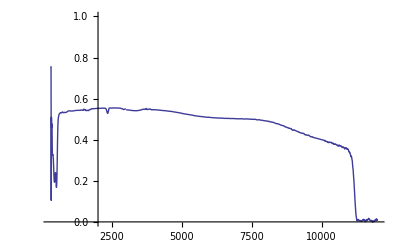

```mathematica
Plot[Abs[trans[sample,v]],{v,301,12000},PlotRange->{{301,12000},{0,1}}]
```

```mathematica
(*Nullstellensuche zur Bestimmung der optischen Konstanten*)
sol=Table[{ν,FindRoot[{transth[ν,n,κ]-Abs[trans[sample,ν]],reflth[ν,n,κ]-Abs[reflex[sample,ν]]},{n,1.2,0,4},{κ,0.001,0,0.1},Compiled->True,DampingFactor->1,MaxIterations->30]},{ν,330,13000,8}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlsemi=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientsemi=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientsemi=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

#### Analysis of GaAs : n-doted

```mathematica
d=440*10^-4;sample=8;
```

```mathematica
sol=Table[{ν,FindRoot[{transth[ν,n,κ]-Abs[trans[sample,ν]],reflth[ν,n,κ]-Abs[reflex[sample,ν]]},{n,1.2,0,6},{κ,0.001,0,0.1},Compiled->True,DampingFactor->1,MaxIterations->60]},{ν,345,13000,8}];
```

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlndot=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientndot=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientndot=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

#### Analysis of Si : semi conducting

```mathematica
d=530*10^-4;sample=9;
```

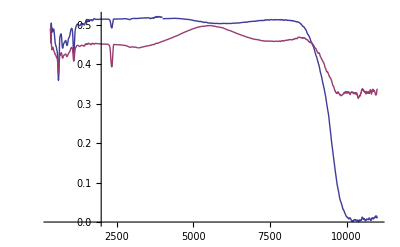

```mathematica
Plot[{trans[sample,ν],reflex[sample,ν]},{ν,350,11000},PlotRange->Full]
```

```mathematica
sol=Table[{ν,FindRoot[{transth[ν,n,κ]-Abs[trans[sample,ν]],reflth[ν,n,κ]-Abs[reflex[sample,ν]]},{n,1,0,6},{κ,0.001,-1,1},Compiled->True,DampingFactor->1,MaxIterations->60]},{ν,320,13000,6}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlsi=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientsi=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientsi=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

#### Analysis of Si : doted

```mathematica
d=530*10^-4;sample=10;
```

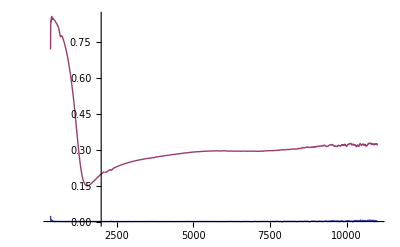

```mathematica
Plot[{trans[sample,ν],reflex[sample,ν]},{ν,350,11000},PlotRange->Full]
```

```mathematica
sol=Table[{ν,FindRoot[{transth[ν,n,κ]-Abs[trans[sample,ν]],reflth[ν,n,κ]-Abs[reflex[sample,ν]]},{n,1,0,6},{κ,0.001,-1,1},Compiled->True,DampingFactor->1,MaxIterations->60]},{ν,350,13000,8}];
```

FindRoot::jsing: Encountered a singular Jacobian at the point {n, κ} = {0., 0.001}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot :: jsing will be suppressed during this calculation.

```mathematica
(*Bildung der Brechzahl aus der Lösung der Nullstellensuche und graphische Darstellung*)
brechzahlsidot=Table[{sol[[j,1]],n/.sol[[j,2]][[1]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{brechzahl},FrameLabel->{"wave numbers (cm^-1)","Brechzahl"},PlotRange->{0,4}]*)
```

```mathematica
(*Bildung des Extinktionskoeffizienten aus der Lösung der Nullstellensuche und graphische Darstellung*)
extinktionskoeffizientsidot=Table[{sol[[j,1]],κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{extinktionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotRange->{{2000,8000},{0,0.0001}}]*)
```

```mathematica
(*Berechnung des Absorptionskoeffizienten und graphische Darstellung*)
absorptionskoeffizientsidot=Table[{sol[[j,1]],4*π*sol[[j,1]]*κ/.sol[[j,2]][[2]]},{j,1,Length[Transpose[sol][[1]]]}];
(*ListPlot[{absorptionskoeffizient},FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotRange->{{2000,8000},{0,5}}]*)
```

### Functions

```mathematica
brechzahlFCTsemi=Interpolation[ExponentialMovingAverage[brechzahlsemi,average],InterpolationOrder->2];
```

```mathematica
extinktionFCTsemi=Interpolation[ExponentialMovingAverage[extinktionskoeffizientsemi,average],InterpolationOrder->2];
```

```mathematica
absorptionFCTsemi=Interpolation[ExponentialMovingAverage[absorptionskoeffizientsemi,average],InterpolationOrder->2];
```

```mathematica
brechzahlFCTndot=Interpolation[ExponentialMovingAverage[brechzahlndot,average],InterpolationOrder->2];
```

```mathematica
extinktionFCTndot=Interpolation[ExponentialMovingAverage[extinktionskoeffizientndot,average],InterpolationOrder->2];
```

```mathematica
absorptionFCTndot=Interpolation[ExponentialMovingAverage[absorptionskoeffizientndot,average],InterpolationOrder->2];
```

```mathematica
plots={brechzahlFCTsemi,extinktionFCTsemi,brechzahlFCTndot,extinktionFCTndot};
```

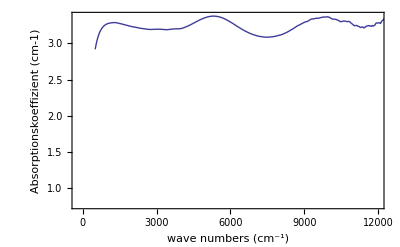
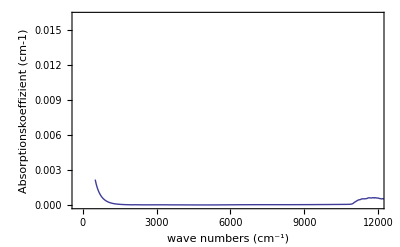
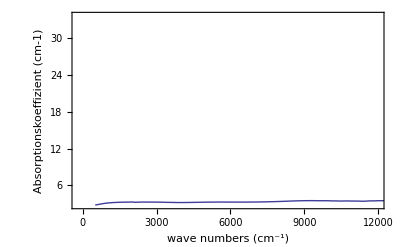
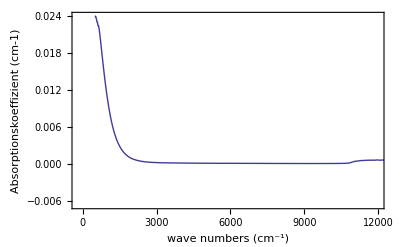

```mathematica
Table[Plot[plots⟦i⟧[x],{x,500,14000},PlotRange->{{-200,12000},All},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient (cm-1)"},PlotStyle->Thick,ImageSize->400],{i,1,4}]
```

```mathematica
brechzahlFCTsi=Interpolation[ExponentialMovingAverage[brechzahlsi,average],InterpolationOrder->2];
extinktionFCTsi=Interpolation[ExponentialMovingAverage[extinktionskoeffizientsi,average],InterpolationOrder->2];
absorptionFCTsi=Interpolation[ExponentialMovingAverage[absorptionskoeffizientsi,average],InterpolationOrder->2];
```

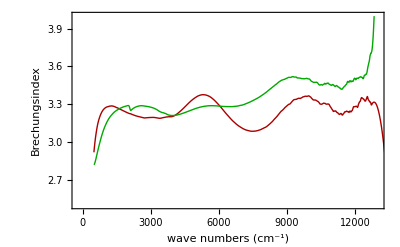

```mathematica
Plot[{brechzahlFCTsemi[x],brechzahlFCTndot[x],brechzahlFCTsi[x]},{x,500,14000},PlotRange->{{-200,13000},{2.5,4}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Brechungsindex"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

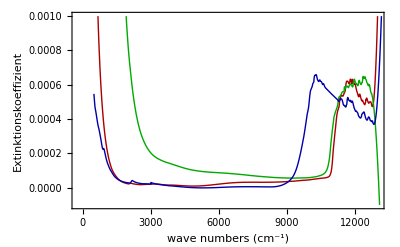

```mathematica
Plot[{extinktionFCTsemi[x],extinktionFCTndot[x],extinktionFCTsi[x]},{x,500,14000},PlotRange->{{-200,13000},{-0.0001,0.001}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Extinktionskoeffizient"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

InterpolatingFunction::dmval: Input value {305.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

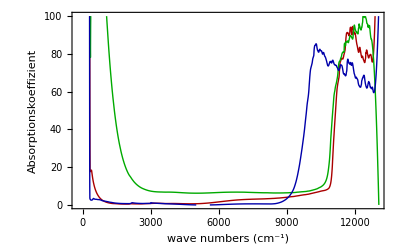

```mathematica
Plot[{absorptionFCTsemi[x],absorptionFCTndot[x],absorptionFCTsi[x]},{x,305,14000},PlotRange->{{-200,13000},{0,100}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Absorptionskoeffizient"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->400]
```

## Drude Modell

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Clear[ref, βabs]
(*Eingabeparameter*)
Print["Trägerdichte in 10^18 cm^-3"]
ne = 1.05
Print["Streuzeit in 10^-12 s"]
τ = 0.1
Print["relative effektive Masse"]
meff = 0.067
Print["relative Dielektrizitätskonstante"]
ϵ∞ = 3.22^2
Print["LO Phononenfrequenz in cm-1"]
νLO = 292
Print["TO Phononenfrequenz in cm-1"]
νTO = 268
Print["Phononendämpfungskonstante in cm-1"]
Γ = 2.5

```mathematica
Clear[ref, βabs,ext,brec,ϵps,σ]
ϵ∞=3.22^2;
νLO=292;
νTO=268;
Γ=2.5;
```

```mathematica
(*Hochfrequenzleitfähigkeit in (Ωm)-1*)
σ[ne_,τ_,meff_]:=28202.2 (ne*τ)/meff 1/(1-I*0.188364*ν*τ);
(*Dielektrizitätsfunktion,x=Skalierungsfaktor für Gitterbeitrag*)
ϵps[x_,ne_,τ_,meff_]:=ϵ∞(1+x*(νLO^2-νTO^2)/(νTO^2-ν^2-I*ν*Γ))+I σ[ne,τ,meff]/(1.66818*ν);

(*Extinktionskoeffizient*)
ext[x_,ne_,τ_,meff_]:=Im[Sqrt[ϵps[x,ne,τ,meff]]];

(*Brechzahl*)
brec[x_,ne_,τ_,meff_]:=Re[Sqrt[ϵps[x,ne,τ,meff]]];

(*Absorptionskoeffizient*)
βabs[x_,ne_,τ_,meff_]:=4*π*ext[x,ne,τ,meff]*ν;
```

Print["Plasmafrequenz in cm-1"]
νp = 299.48 Sqrt[ne/(meff*ϵ∞)]

Print["Frequenz der oberen Plasmon-Phonon-Mode in cm-1"]
νpp = Sqrt[1/2 (νLO^2 + νp^2) + 1/2 Sqrt[(νLO^2 + νp^2)^2 - 4*νp^2*νTO^2]]

Print["Frequenz der unteren Plasmon-Phonon-Mode in cm-1"]
νpm = Sqrt[1/2 (νLO^2 + νp^2) - 1/2 Sqrt[(νLO^2 + νp^2)^2 - 4*νp^2*νTO^2]]

```mathematica
(*Reflexion am Halbraum*)
rh[x_,ne_,τ_,meff_]:= Abs[(Sqrt[ϵps[x,ne,τ,meff]] - 1)/(Sqrt[ϵps[x,ne,τ,meff]] + 1)]^2;
```

```mathematica
(*Reflexion einer planparallelen Schicht*)
ref[x_,d_,ne_,τ_,meff_]:=rh[x,ne,τ,meff] (1+Exp[-2*βabs[x,ne,τ,meff]*d]-2*rh[x,ne,τ,meff]*Exp[-2*βabs[x,ne,τ,meff]*d])/(1-(rh[x,ne,τ,meff]^2)*Exp[-2*βabs[x,ne,τ,meff]*d]);
```

### GaAs dotiert

```mathematica
βexp=absorptionFCTndot;
reflintga[ν_]:=reflex[8,ν]
```

```mathematica
(*Vergleich des Experiments mit der Theorie (mit Gitterbeitrag)*)
Manipulate[Plot[{ref[1,640*10^-4,ne,τ,meff],reflintga[ν]},{ν,350,3000},PlotRange->{{0,3000},{0,0.5}},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLegend->{"theory, 440 µm","experiment"},LegendPosition->{1,-0.3},LegendShadow->{0,0},PlotLabel->"n-dot-GaAs, ϵ(ω) mit Gitterbeitrag ",ImageSize->800],{{ne,0.9},0.70,2.00,0.1},{{τ,0.1},0.2,0.001,0.005},{{meff,0.06},0.05,0.08,0.005}]
```

```mathematica
(*Vergleich des Experiments mit der Theorie (mit Gitterbeitrag)*)
Manipulate[Plot[{ref[1,640*10^-4,ne,τ,meff],reflintga[ν]},{ν,350,3000},PlotRange->{{0,3000},{0,0.5}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->800,PlotLegends->{"Theorie","Experiment"}],{{ne,0.9},0.70,2.00,0.1},{{τ,0.1},0.2,0.001,0.005},{{meff,0.06},0.05,0.08,0.005}]
```

### Si dotiert

```mathematica
reflintsi[ν_]:=reflex[10,ν]
```

```mathematica
(*Vergleich des Experiments mit der Theorie (mit Gitterbeitrag)*)
Manipulate[Plot[{ref[1,640*10^-4,nne,nτ,nmeff],reflintsi[ν]},{ν,350,2800},PlotRange->{{0,3000},{0,0.5}},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLegend->{"theory, 440 µm","experiment"},LegendPosition->{1,-0.3},LegendShadow->{0,0},PlotLabel->"n-dot-GaAs, ϵ(ω) mit Gitterbeitrag ",ImageSize->800],{{nne,1.1},0.9,1.40,0.05},{{nτ,0.0095},0.0005,0.015,0.005},{{nmeff,0.0055},0.0005,0.008,0.0005}]
```

```mathematica
(*Vergleich des Experiments mit der Theorie (mit Gitterbeitrag)*)
Manipulate[Plot[{ref[1,640*10^-4,nne,nτ,nmeff],reflintsi[ν]},{ν,350,2800},PlotRange->{{0,3000},{0,0.5}},Frame->True,FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},ImageSize->800],{{nne,1.1},0.9,1.40,0.05},{{nτ,0.0095},0.0005,0.015,0.005},{{nmeff,0.0055},0.0005,0.008,0.0005}]
```